```mathematica
BISECTION METHOD

Ques1.Find the root of x^3+4x+1 = 0 approximately upto 25 iterations using Bisection  Method. Let X[0] = -2 and X[1] = 0. Also Plot the Graph.
```

1th iteration value is : -1

Estimated error in 1th iteration is : 1

2th iteration value is : -1/2

Estimated error in 2th iteration is : 1/2

3th iteration value is : -1/4

Estimated error in 3th iteration is : 1/4

4th iteration value is : -1/8

Estimated error in 4th iteration is : 1/8

5th iteration value is : -3/16

Estimated error in 5th iteration is : 1/16

6th iteration value is : -7/32

Estimated error in 6th iteration is : 1/32

7th iteration value is : -15/64

Estimated error in 7th iteration is : 1/64

8th iteration value is : -31/128

Estimated error in 8th iteration is : 1/128

9th iteration value is : -63/256

Estimated error in 9th iteration is : 1/256

10th iteration value is : -127/512

Estimated error in 10th iteration is : 1/512

Return[-253/1024]

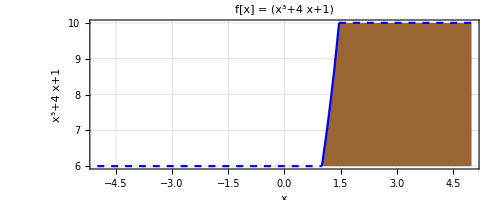

```mathematica
x0 = -2;
x1 = 0;
Nmax = 25;
eps = 0.001; 
f[x_] := x ^3 + 4x + 1; If[N[f[x0] * f[x1]] > 0, 
Print["These values do not satisfy the IVP so change the values."],
For [i = 1, i ≤ Nmax, i++, a = (x0 + x1) / 2; 
If[Abs[(x1 - x0) / 2] < eps, Return[a],
Print[i, "th iteration value is : ", a]; 
Print[" Estimated error in ", i, "th iteration is : ", (x1 - x0) / 2]; 
If[f[a] * f[x1] > 0, x1 = a, x0 = a]]];
Print[" Root is : ", a];
Print[" Estimated error in ", i, "th iteration is : ", (x1 - x0) / 2]] 
Plot[f[x], {x, -5, 5}, PlotRange -> {10, 6}, 
PlotStyle -> Blue, PlotLabel -> "f[x] = " f[x], AxesLabel -> {x, f[x]},
AspectRatio -> Automatic, Frame -> True, GridLines -> Automatic,
ClippingStyle -> Automatic, Filling -> Axis, FillingStyle -> Brown]
```

SECANT METHOD

```mathematica
Question 2. Perform 5 iterations using Secant method to find the root of the equation x^5-8x+8=0.
```

```mathematica
f[x_] := x ^5 - 8 * x + 8
x0 = 0;x1 = 1;
n = 5; list = {};
For[i = 1, i ≤ n, i++, x2 = (x0 * f[x1] - x1 * f[x0]) / (f[x1] - f[x0]);
list = Append[list, {i, x0, x1, x2, f[x2]}];
x0 = x2];
Print[TableForm[N[list], 
TableHeadings -> {None, {"No. Of Iterations ", "x0", "x1", "Approxiate Root", "f[x2]"}}]]
```

1. | 0. | 1. | 1.14286 | 0.806807
2. | 1.14286 | 1. | 1.73945 | 10.0087
3. | 1.73945 | 1. | 0.917918 | 1.30831
4. | 0.917918 | 1. | 1.26623 | 1.12525
5. | 1.26623 | 1. | -1.12565 | 15.198

NEWTON RAPHSON METHOD

```mathematica
Question 3.The equation f(x) is given as x^2-2x-1=0. Considering the initial guess at x=4 then the value of next approximation.Also plot graph.
```

```mathematica
x0 = Input["Enter initial guess : "];
Nmax = Input["Enter maximum number of iterations : "];
eps = Input["Enter a value of convergence parameter : "]; 
Print["x0=", x0]
```

x0=4

```mathematica
Print["Nmax=", Nmax]
```

Nmax=1

```mathematica
Print["epsilon=", eps]
```

epsilon=2

```mathematica
f[x] := x ^2 - 2 x - 1; 
Print["f(x) := ", f[x]]
```

f(x) := -1-2 x+x^2

```mathematica
Print["f'(x):= ", f'[x]]
```

f'(x):= f'[x]

```mathematica
f[x_] := x ^2 - 2 x - 1;
Print["f'(x):= ", f'[x]]
```

f'(x):= -2+2 x

```mathematica
For[i = 1, i ≤ Nmax, i++, x1 = N[x0 - (f[x] /. x -> x0) / (f '[x] /. x -> x0)];
If[Abs[x1 - x0] < eps, Return[x1], x0p = x0; x0 = x1];
Print["In ", i , "th Number of iterations the approximation to root is : ", x1];
Print[" Estimated error is : ", Abs[x1 - x0]]]
```

2.83333

```mathematica
Print["the final approximation of root is : ", x1]
```

the final approximation of root is : 2.83333

```mathematica
Print[" Estimated error is : ", Abs[x1 - x0]]
```

Estimated error is : 1.16667

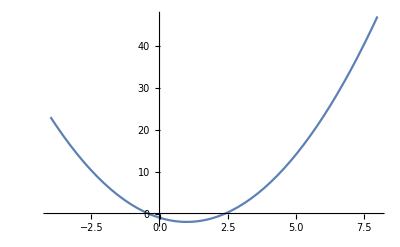

```mathematica
Plot[f[x], {x, -4, 8}]
```

GAUSS JORDAN METHOD

Question 4.  Solve the system of equations by Gaussian elimination method :
			
                           1x1 + 2 x2 + 2x3 = -2
			6x1 + 7x2 + 5x3 = 1
			2x1 + 6x2 + 2x3 = 7

```mathematica
A1 = {{1, 6, 2}, {2, 7, 6}, {2, 5, 2}};
b1 = {-2, 1, 7}; 
aug = Transpose[Append[Transpose[A1], b1]]; 
MATRIX = RowReduce[aug];
sol = Take[MATRIX, 3, {4}] // MatrixForm
```

(23/3
-4/3
-5/6)

Therefore x1=23/2, x2=-4/3 & x3=-5/6

```mathematica
JACOBI METHOD
```

```mathematica
Question 5. Solve the system of equations by Jacobi method : 

 1x1 + 7 x2 + 1x3 = 1 
 1x1 + 2 x2 + 1x3 = 2 
1x1 + 4x2 + 1x3 = 3
```

```mathematica
xold = {0, 0, 0};
A = {{1, 7, 1}, {1, 2, 1}, {1, 4, 1}};
b = {1, 2, 3};
d = {{1, 0, 0}, {0, 2, 0}, {0, 0, 1}};
L = LowerTriangularize[A] - d;
U = UpperTriangularize[A] - d; 
di = Inverse[d]; 
K = -(L + U);
For[i = 0, i ≤ 2, i++; 
xnew = di.K.xold + di.b; 
xold = xnew; 
Print[N[xnew]]]
```

{1.,1.,3.}

{-9.,-1.,-2.}

{10.,6.5,16.}

```mathematica
Lagrange Interpolation
```

Question 6.  Given that f(5)=12, f(6)=13,and f(9)=14. Find the Lagrange Polynomial of degree 2 using given data and
                          also find f(10).

```mathematica
No = 3; sum = 0; 
lagrange[No_, n_] :=
Product[If[Equal[k, n], 1, (x - x[k]) / (x[n] - x[k])], {k, 1, No}]; 
For[i = 1, i ≤ No, i++, sum += (f[x[i]] * lagrange[No, i])];
Print[sum]
```

((-1-2 x[1]+x[1]^2) (x-x[2]) (x-x[3]))/((x[1]-x[2]) (x[1]-x[3]))+((x-x[1]) (-1-2 x[2]+x[2]^2) (x-x[3]))/((-x[1]+x[2]) (x[2]-x[3]))+((x-x[1]) (x-x[2]) (-1-2 x[3]+x[3]^2))/((-x[1]+x[3]) (-x[2]+x[3]))

```mathematica
sum = 0; 
points = {{5, 12}, {6, 13}, {9, 14}};
No = Length[points]
y = points[[All, 1]] 
f = points[[All, 2]] 
lagrange[No_, n_] := 
Product[If[Equal[k, n], 1, (x - y[[k]]) / (y[[n]] - y[[k]])], {k, 1, No}] 
For[i = 1, i ≤ No, i++, sum += (f[[i]] * lagrange[No, i])]
Expand[sum] 
sum /. x -> 10
```

3

{5,6,9}

{12,13,14}

2+(17 x)/6-x^2/6

41/3

```mathematica
TRAPEZOIDAL RULE
```

```mathematica
Question 7. Approximate the area under the curve y=1/x between x=1 and x=5 using the Trapezoidal rule with n=4 subintervals.
```

```mathematica
ClearAll[n, x, f] 
a = Input["Enter the left end point : "] 
b = Input["Enter the right end point : "] 
n = Input["Enter the number of sub intervals to be formed : "] 
sum = 0 
h = (b - a) / n 
f[x] = 1 / x 
For[i = 1, i ≤ n - 1, i++, sum += N[f[x] /. x -> (a + i * h)]] 
sum = N[(2 * sum + f[x] /. x -> a + f[x] /. x -> b) * h / 2]
```

1

5

4

0

1

1/x

1.5

```mathematica
EULER METHOD
```

```mathematica
Question 8. Find the value of y (0.8) by using Euler’ s Method of the initial value problem dy/dx=y+7 xy,y (0)=0.5.
```

```mathematica
f[x_, y_] := y + 7 * x * y; 
a = 0;
b = 0.8;
h = 0.2; 
n = (b - a) / h;
y[0] = 0.5; 
For[i = 0, i ≤ n - 1, i++, x[i] = a + i * h; 
y[i + 1] = y[i] + h * f[x[i], y[i]]; 
Print[y[i + 1]]]
```

{5,6,9}[1]

{5,6,9}[2]

{5,6,9}[3]

{5,6,9}[4]

```mathematica
THANK YOU
```